## Метод срединных квадратов

```mathematica
nMax=100;
sqr[x_]:=Quotient[Mod[x^2+x+1,10000],10];
t[y_]:=RecurrenceTable[{X[n+1]==sqr[X[n]],X[1]==y},
X,
{n,1,nMax}
];
t[132]
```

{132,742,56,313,797,521,144,73,533,409,728,998,600,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
t[2]
```

{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Графики последовательностей с разными начальным значением

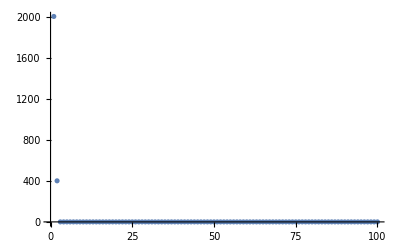
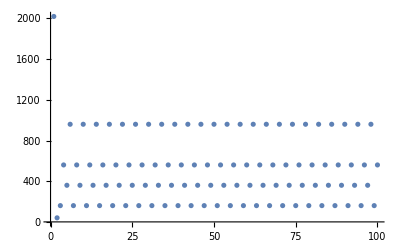
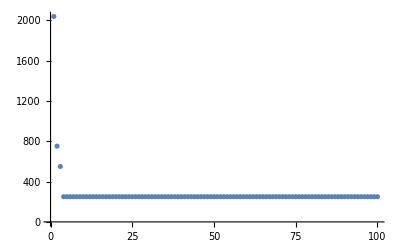
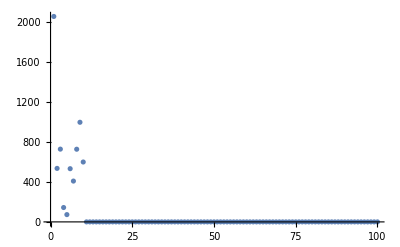
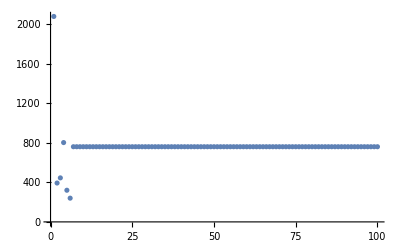
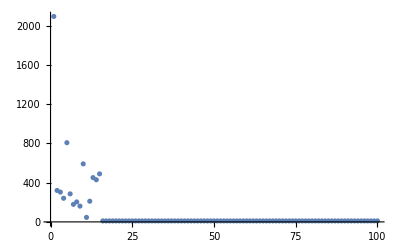
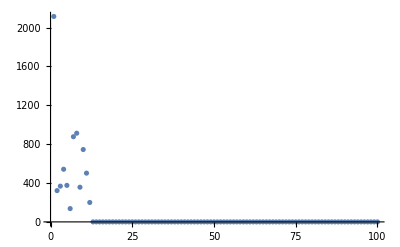
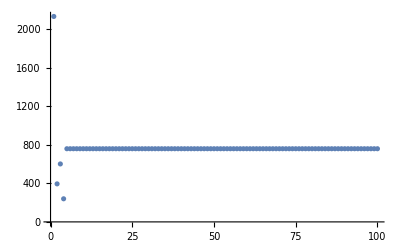

```mathematica
Table[
ListPlot[t[s]],{s,2001,4001,19}
]
```